# 透過機器學習分類咳嗽聲，以準確預測新冠肺炎。

## Abstract:

聲音的分類是一項艱鉅的任務，尤其是當聲音樣本中有非常微小的變化，使我們人類的耳多難以察覺。
電腦的使用以及近年來的機器學習模型已被證實是解決聲音分類問題的有效方法。
這些ML程序可以幫助改善診斷準確性，並且已經成為心臟病學和肺病學等領域的研究主題。
近來的機器學習應用創新，例如說用卷積神經網路(CNN)來識別COVID-19咳嗽，
和麻省理工AI團隊使用咳嗽紀錄檢測無症狀COVID-19感染者的AI模型，他的的AI模型驗證了一些非常有希望且準確的結果，僅僅是通過咳嗽的聲音。
我們觀察一下這些References... 看似是一項非常具有挑戰性的任務，就像是頂尖的研究人員才能夠完成的事情。
在此篇實作中，我將跟各位討論如何使用Wolfram Language中的高階機器學習語言和音頻分析Functions來獲得一些非常fantastic的結果!~

## Introduction

使用labeling的 COVID-19的開源咳嗽聲音數據集，我們自訂義建構了一個循環神經網路(RNN)，並使用Mei頻率倒譜係數(MFCC)進行特徵提取(features extration)輸入預處理(Unstructured Data Preprocessing)後的音頻訊號。
最後會展示結果，結果顯示這種方法大約為我們提供了96%的準確率，這種結果非常近似於其他已發表的國際期刊。
即便，我們的方法只用了121少量的樣本數。

### Data

我們使用的數據包含121個 . mp3格式的咳嗽聲音分段樣本。都是可以公開取得的。
在121個樣本數據裡面，我們分為兩類。
 一類是來自COVID-19檢測呈陽性的患者共48位，一類是COVID-19檢測為陰性的患者共73位。

## 主要內文，包含實際WolframCoding

### 載入數據, 然後分割訓練集(TrainingSet)和測試集(TestingSet)

```mathematica
data=KeyValueMap[Map[Reverse,Thread[#1->#2]]&]@AssociationMap[Map[Import,Flatten[StringCases[Import["https://github.com/virufy/virufy_data/tree/main/clinical/segmented/"<>#,"Hyperlinks"],"https://github.com/virufy/virufy_data/blob/main/clinical/segmented/"<>#<>"/"~~x__:>"https://raw.githubusercontent.com/virufy/virufy_data/main/clinical/segmented/"<>#<>"/"<>x]]]&,{"pos","neg"}]//Flatten;
```

```mathematica
Counts[Values[data]]
```

```mathematica
<|"pos"->48,"neg"->73|>
```

例如，下列是這兩類資料個別隨機取出的咳嗽聲音：

```mathematica
RandomSample[data,2]
```

{→neg,→pos}

雖然樣本量不太平衡，但差異算很小，模型仍應有效。
我們使用Wolfram的Functions存儲庫中的TrainTestSplit，以分別創建訓練集和測試集。
在Mathematica預設的情況下，它將數據拆分為 80 %訓練集和 20 % 的測試集：

```mathematica
{train,test}=ResourceFunction["TrainTestSplit"][data];
```

### Audio Encoding

音訊編碼(Audio encoding)是音訊分類的重要步驟，因為人類產生的任何聲音都由其聲帶的形狀決定。如果這個形狀可以正確決定，任何產生的聲音都可以被準確表示。
樂器也是如此：即使兩種不同的樂器可以產生相同的音訊，它們也會因為樂器的物理特性（鋼琴、吉他、長笛等）而聽起來不同。
語音信號的時間功率頻譜波包即為聲帶的代表，MFCCs 可以準確地表達此聲帶概念。
一些疾病，例如肺部疾病，會影響空氣通過我們呼吸系統的運行方式，可能因此就會導致健康者和患病患者之間存在著聲音上的差異：

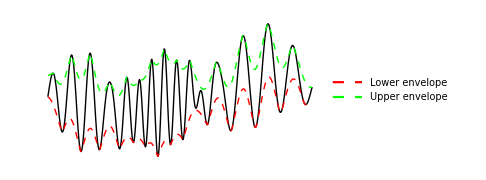

為了獲得 MFCCs，我們首先會在時域上對原始聲波應用傅立葉轉換，
然後對結果頻譜應用幅度的對數，最後再應用餘弦轉換。
最後得到的頻譜，稱為在quefrency domain中的倒頻譜(cepstrum)，既不在頻域也不在時域。

我們將使用 NetEncoder方法中的“AudioMFCC”選項來使整個過程自動化。
我們還可以使用“NumberOfCoefficients”選項在結果中選擇我們想要的係數數量：

```mathematica
encoder=NetEncoder[{"AudioMFCC","TargetLength"->All,"NumberOfCoefficients"->40,"SampleRate"->16000,"WindowSize"->1024,"Offset"->571,"Normalization"->"Max"}]
```

NetEncoder[<>]

我們可以檢查 "AudioMFCC" 和 NetEncoder 應用於隨機音頻樣本的結果。
編碼器的輸出是一個維度為 {n,40} 的 2 階張量，其中 n 是應用預處理後的分區數，40 是用於計算的係數數量：

```mathematica
MatrixPlot[encoder[Audio[RandomChoice[Keys[train]]]]]
```

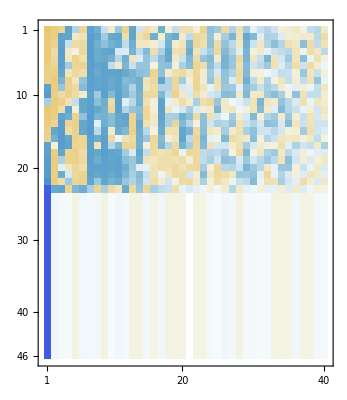

我們可以看到音頻是如何被轉換成表示音頻倒譜特徵的矩陣的。
且這將是我們模型的輸入。
在此將構建一個自定義循環神經網絡 (RNN)，手動調整超參數(hyperparameters)，在調整(tune)-訓練(train)-評估(validate)過程中對神經網路RNN進行Optimization iteration。
這意味著 RNN 將：（1）選擇一組超參數；(2) 訓練模型；(3) 評估模型；(4) 重複步驟一到三。我們重複這個過程，直到模型顯示出低Overfitting和高評估指標。
結果是以下RNN：

### 自訂義RNN模型

```mathematica
rnn=NetChain[{GatedRecurrentLayer[12,"Dropout"->{"VariationalInput"->0.2}],
SequenceLastLayer[],LinearLayer[2],DropoutLayer[.5],Ramp,LinearLayer[],SoftmaxLayer[]},"Input"->encoder,"Output"->NetDecoder[{"Class",{"pos","neg"}}]]
```

NetChain[<>]

我們通過訓練集訓練RNN，並在測試集上進行驗證。
這使我們能夠觀察訓練過程並調整RNN model的超參數，
例如線性層上的神經元量、DropoutLayer 編號和GatedRecurrentLayer的序列特徵量：

```mathematica
resultObjectRNN=NetTrain[rnn,train,All,ValidationSet->test]
```

NetTrain Results
summary | ,,  batches:1328  rounds:332  time:33s  examples/s:1317
data | ,,  training examples:97  validation examples:24  processed examples:42496  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:4.01×10^-1  error:19.5%
validation | ,,  loss:4.05×10^-1  error:12.5%
 | 
-Graphics-  training set	-Graphics-  validation set |

訓練結束后，我們將對模型進行評估(metric)，將其應用模型從來沒看過的資料上，即測試數據集並測量其各種性能。
為此，我們將嘗試不同的指標諸如...：

Accuracy: 被正確預測的觀測結果與母體觀測結果的比例。

F1 score:  precision和recall 的平均權重分布.

Precision and recall:

Confusion matrix plot:

ROC curve: 告訴我們模型準確區分類別的能力（見下圖）。 負類和正類曲線之間的重疊越大，ROC 曲線就越差。 最佳 ROC 曲線是曲線下面積 (AUC) 等於 1 的曲線。

```mathematica
Grid[{Style[#,Bold]&/@{"Accuray","F1 Score","Precision","Recall"},NetMeasurements[resultObjectRNN["TrainedNet"],test,{"Accuracy","F1Score",<|"Measurement"->"Precision","ClassAveraging"->"Macro"|>,<|"Measurement"->"Recall","ClassAveraging"->"Macro"|>}]},Frame->All]
```

Accuray | F1 Score | Precision | Recall
0.958333 | <|pos→0.933333,neg→0.969697|> | 0.9375 | 0.970588

We can also plot the confusion matrix and ROC curve of the model applied to the test set:

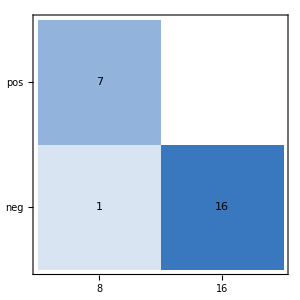
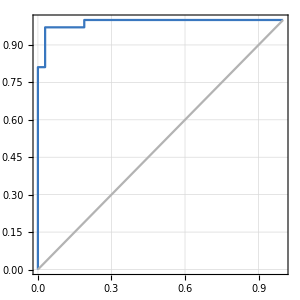
actual class | -Graphics-
 | predicted classrecall | -Graphics-
 | false positive rate

```mathematica
Row@NetMeasurements[resultObjectRNN["TrainedNet"],test,{"ConfusionMatrixPlot","ROCCurvePlot"}]
```

總體而言，我們通過評估的指標獲得了出色的表現。
這些評估指標告訴我們，該模型能夠從患者的咳嗽聲中正確識別或排除 COVID-19 的存在與否。

此項目構建了一個基於RNN的模型，該模型能夠通過以 96% 左右的準確率對咳嗽聲音進行分類來檢測 COVID-19。 
這不僅顯示了RNN在解決聲音分類任務方面的能力，而且還顯示了解決諸如診斷肺部疾病等醫療任務的潛力。
 這個任務微重現了麻省理工AI團隊發布文章的實驗方法和不凡的結果。 
 我們的數據集很小（只有121 個samples），但結果卻很準確，可謂此項目為未來的研究開闢了無限的可能性。

Get full access to the latest Wolfram Language functionality with a Mathematica 12.3 or Wolfram|One trial.